# Question 01

ⅇ^(-Sin[x]) C[1]

{-5 ⅇ^(-Sin[x]),-4 ⅇ^(-Sin[x]),-3 ⅇ^(-Sin[x]),-2 ⅇ^(-Sin[x]),-ⅇ^(-Sin[x]),0,ⅇ^(-Sin[x]),2 ⅇ^(-Sin[x]),3 ⅇ^(-Sin[x]),4 ⅇ^(-Sin[x]),5 ⅇ^(-Sin[x])}

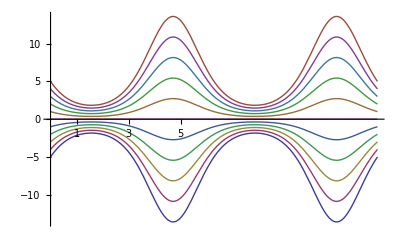

```mathematica
eq=DSolve[y'[x]==-Cos[x]*y[x],y[x],x][[1,1,2]]
table1=Table[eq/.C[1]->i,{i,-5,5}]
Plot[table1,{x,0,4*Pi},Ticks->{{1,2,3,4,5,6},{}}]
```

# Question 02

x[t]+x'[t] (-1+1/3 x'[t]^2)+x''[t]==0

{InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t]}

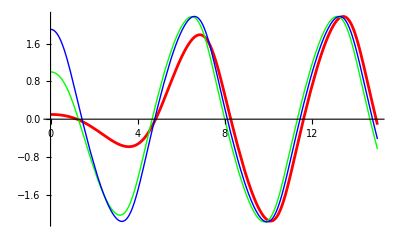

```mathematica
eq=x''[t]+(x'[t]^2/3-1)*x'[t]+x[t]==0
table2=Table[NDSolveValue[{eq,x[0]==k,x'[0]==0},x[t],{t,0,15}],{k,.1,1.9,.9}]
Plot[table2,{t,0,15},PlotStyle->{{Red,Thickness[.005]},Green,Blue}]
```

# Question 03

{InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t]}

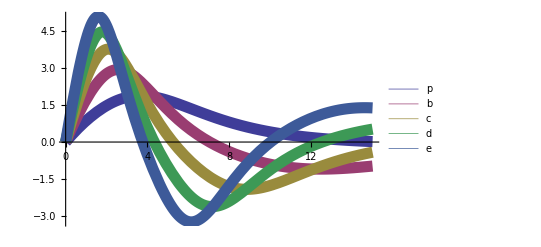

```mathematica
m=1;k=.3;a=.04;
table3=Table[NDSolveValue[{m*x''[t]+k*x'[t]+a*x[t]^3==0,x[0]==0,x'[0]==i},x[t],{t,0,15}],{i,5}]
Plot[table3,{t,0,15},PlotLegends->{p,b,c,d,e},PlotStyle->Thickness[.02]]
```

# Problem 04

```mathematica
s=10;b=8/3;p=28;
table4=NDSolveValue[{x'[t]==s*(y[t]-x[t]),y'[t]==p*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==10,y[0]==10,z[0]==10},{x[t],y[t],z[t]},{t,0,50}]
```

{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]}

```mathematica
ParametricPlot3D[table4,{t,0,50}]
```

-Graphics3D-

# Question 05

{{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]},{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]},{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]},{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]},{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]},{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]},{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]}}

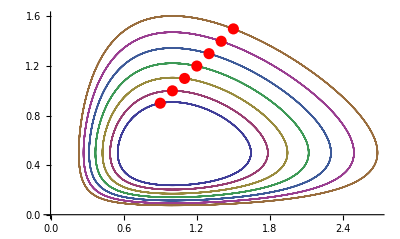

```mathematica
a=2/3; b=4/3; g=1;d=1;
table5=Table[NDSolveValue[{x'[t]==x[t]*(a-b*y[t]),y'[t]==y[t]*(d*x[t]-g),x[0]==i,y[0]==i},{x[t],y[t]},{t,0,50}],{i,.9,1.5,.1}]
g1=ParametricPlot[table5,{t,0,50}];
g2=ListPlot[Table[{i,i},{i,.9,1.5,.1}],PlotStyle->{Red,PointSize[.02]}];
Show[g1,g2]
```

# Question 06

```mathematica
Exit[]
```

```mathematica
eq=D[u[x,t],{x,2}]==D[u[x,t],{t,2}]
init={u[x,0]->3*x,Derivative[0,1][u][x,0]->Sin[2*x]}
lp=LaplaceTransform[eq,t,s]/.init
sol=DSolve[lp,u[x,t],x][[1,1,2]]
ilp=InverseLaplaceTransform[sol,s,t]
Plot3D[ilp,{x,-5,5},{t,0,5},ColorFunction->"Rainbow"]
```

u^(2,0)[x,t]==u^(0,2)[x,t]

{u[x,0]→3 x,u^(0,1)[x,0]→Sin[2 x]}

LaplaceTransform[u^(2,0)[x,t],t,s]==-3 s x+s^2 LaplaceTransform[u[x,t],t,s]-Sin[2 x]

ⅇ^(s x) C[1]+ⅇ^(-s x) C[2]+(12 x+3 s^2 x+s Sin[2 x])/(4+s^2)

C[2] DiracDelta[t-x]+C[1] DiracDelta[t+x]+3 x (DiracDelta[t]-2 Sin[2 t])+6 x Sin[2 t]+Cos[2 t] Sin[2 x]

-Graphics3D-